## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
```

## Compare with other Brito el al. data

```mathematica
ZBCP=GroupBy[{N@Round[#1,10^-5.],#2(1+Sqrt[1-#1^2]),#3}&@@@Import@GetZFileBCP[-1,1,1],First->(Drop[#,1]&)];
```

Compare s=1 data

```mathematica
Z0=GroupBy[{N@Round[#1,10^-5.],#2,#3}&@@@Import@GetZFile[1,1,1,"detailed"],First->(Drop[#,1]&)];
Z2=GroupBy[{N@Round[#1,10^-5.],#2,#3}&@@@Import@GetZFile[-1,1,1,"detailed"],First->(Drop[#,1]&)];
```

```mathematica
sameJ=Intersection[Keys@ZBCP,Keys@Z0];
```

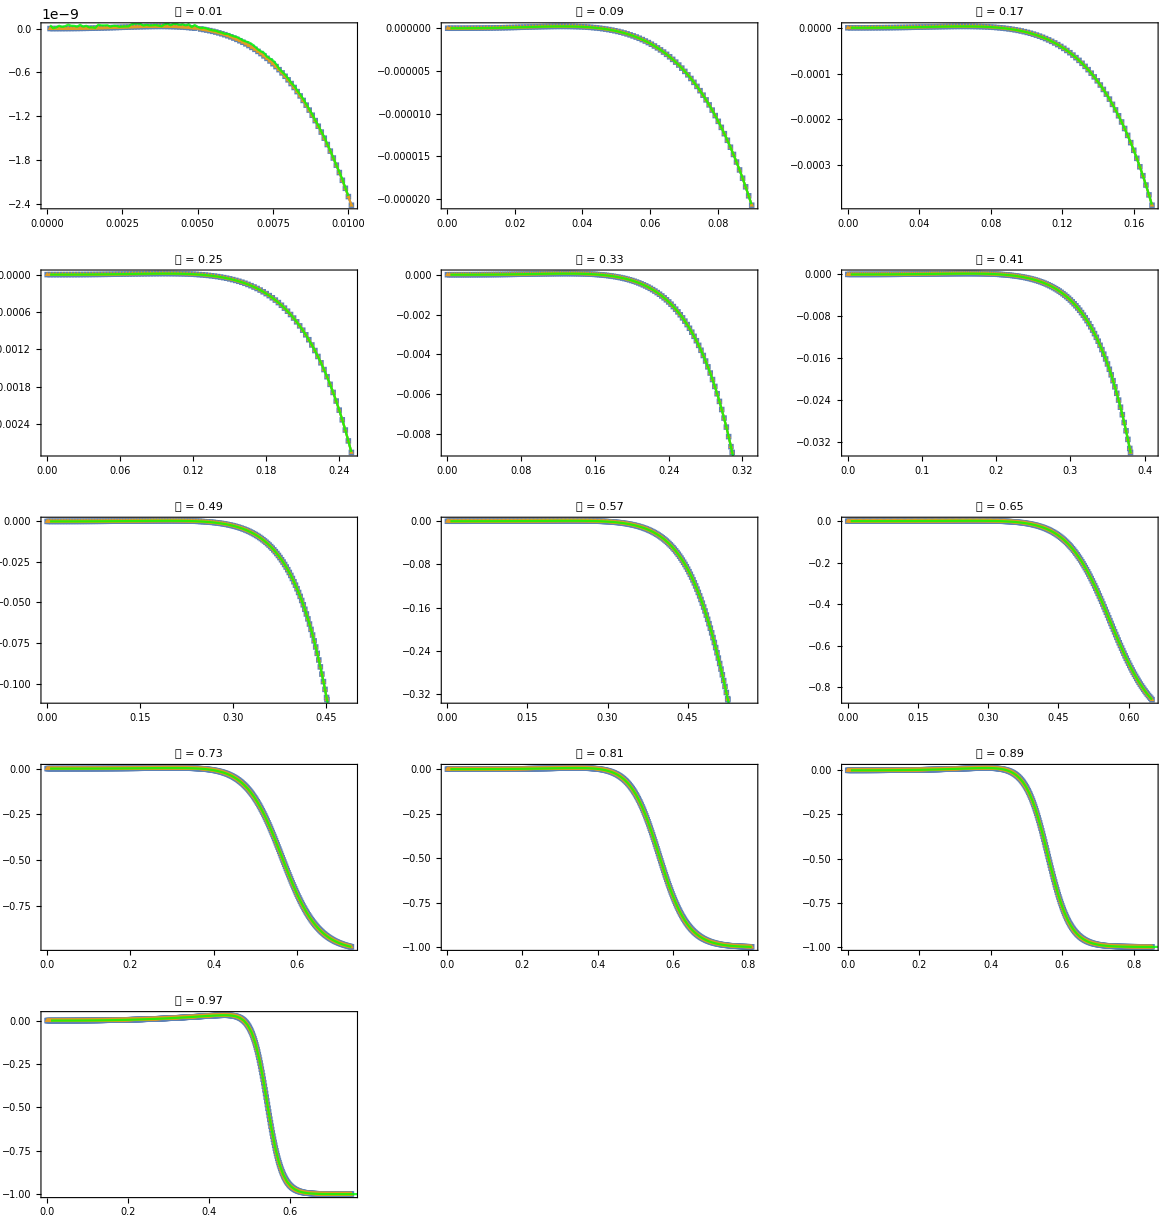

```mathematica
Show[
ListPlot[Z0[#],Joined->True,PlotStyle->ColorData[97,1],PlotMarkers->{■,Small}],
ListPlot[Z2[#],Joined->True,PlotStyle->ColorData[97,2],PlotMarkers->{▲,Small}],
ListPlot[ZBCP[#],Joined->True,PlotStyle->{Opacity[0.8],Green}],
ImageSize->Medium,PlotLabel->StringRiffle[{"𝒥","=",#}," "],Frame->True
]&/@Take[sameJ,{1,Length@sameJ,8}]//GraphicsGrid@Partition[#,3,3,1,{}]&
```